```mathematica
SineDepth=128;(*Number of entries in the table*)
SineWidth=14;(*bit width of each entry*)
(*twoscomplement[n_,bits_:32]:=If[n≥0,IntegerDigits[n,2,bits],1-IntegerDigits[2^bits-n+1,2,bits]]; THIS CODE DOES NOT WORK PROPERLY!*)
twoscomplement[n_,bits_:32]:=If[Positive[n],IntegerDigits[n,2,bits],IntegerDigits[FromDigits[IntegerDigits[n,2,bits]/.{1->0,0->1},2]+1,2,bits]]
SineTable=Table[Round[(2^(SineWidth-1.)-1)Sin[2.π jj/SineDepth]],{jj,0,SineDepth-1}];
CosineTable=Table[Round[(2^(SineWidth-1.)-1)Cos[2.π jj/SineDepth]],{jj,0,SineDepth-1}];
SetDirectory[NotebookDirectory[]];
Export["sinetable"<>ToString[SineDepth]<>"x"<>ToString[SineWidth]<>"bit.txt",IntegerString[FromDigits[twoscomplement[#,SineWidth],2],16]&/@SineTable]
Export["cosinetable"<>ToString[SineDepth]<>"x"<>ToString[SineWidth]<>"bit.txt",IntegerString[FromDigits[twoscomplement[#,SineWidth],2],16]&/@CosineTable]
```

sinetable128x14bit.txt

cosinetable128x14bit.txt

128

128

8191

8191

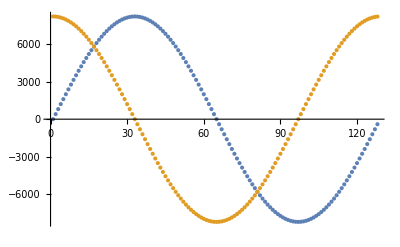

```mathematica
Length[SineTable]
Length[CosineTable]
Max[SineTable]
Max[CosineTable]
ListPlot[{SineTable,CosineTable}]
```